# NV-center qubits

## Connectivity : star Main ref: Abobeih

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

NV-center device, loaded after questlink

```mathematica
Get["../vqd.wl"];
```

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second
Frequency unit is  Hertz
Each qubit has unique characteristics

```mathematica
Options[NVCenterDelft]={
qubitsNum->6,
(** passive noise forms **)
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>,
(* we assume T2* echoed out to T2*)
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>,
(* cross-talk ZZ-coupling in order of Hz on passive noise, Phase entanglement among nuclear spin. Weak ZZ-coupling. Few Hz *)
FreqWeakZZ->5,
(*GlobalField-><|#->RandomReal[{-0.01,0.01}]&/@Range[0,5]|>,
GlobalFieldDetuning->66000,*)

(* rates are Hz. Direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins?*)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>,

(* 2-qubit gates can be done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>,
(* approx 95-99 *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>,
(* fidelities are in percent and is obtained from random becnhmarking by default *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>,
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,6->0.99 |>,
(** Error ratio {depolarizing error, dephasing ratio}, where the ratios are sum to one. characterizes inhomogenieties between depolarizing and dephasing noises **)
(* For single rotations *)
EFSingleXY->{0.75,0.25},
(* For conditional rotations CRx and CRy. Note that, applying single rotations on nuclear spins mean applying conditional rotations *)
EFCRot->{0.9,0.1},
(** Initialization and destructive measurement on the electron spin.
nuclear spin init and measurement are done on the electron-spin through swap sequence **)
FidInit-> 0.999,
DurInit->2*10^-3,
(** measurements **)
FidMeas->0.946,
(* 10-20 μs *)
DurMeas->2*10^-5
};
```

## Introduction to essential elements

```mathematica
nvnode=NVCenterDelft[];
```

The native gates:

```mathematica
nvnode[Gates]⟦All,1⟧//Column
```

Init_(VQD`Private`q$_)/;VQD`Private`q$===0
M_(VQD`Private`q$_)/;VQD`Private`q$===0
Wait_(VQD`Private`qubits$__)[VQD`Private`dur$_]
Rz_(VQD`Private`q$_)[VQD`Private`θ$_]
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$===0
Rx_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
Ry_(VQD`Private`q$_)[VQD`Private`θ$_]/;VQD`Private`q$>0
CRx_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0
CRy_(VQD`Private`e$_,VQD`Private`n$_)[VQD`Private`θ$_]/;VQD`Private`e$==0&&VQD`Private`n$>0

## Common gates on nuclear spins obtained by sequence of native gates

```mathematica
(* cotrolled-pauli gates, where control qubits are the electron spins *)
Subscript[cX, c_,t_]:=Sequence@@{Subscript[CRx, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]}
Subscript[cY, c_,t_]:=Sequence@@{Subscript[CRy, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][-π/2]}
Subscript[cZ, c_,t_]:=Sequence@@{Subscript[Rx, t][π/2],Subscript[CRy, c,t][-π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][π/2],Subscript[Rx, t][-π/2]}
(* initialisation the nuclear spins *)
Subscript[initNcl, q_/;q>0]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2]}
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_/;q>0]:=Sequence[Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]]
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2]}

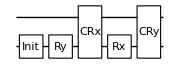

```mathematica
{Subscript[initNcl, 1]}
DrawCircuit@%
```

## 6 Qubits initialization

Initialize all qubits to zero

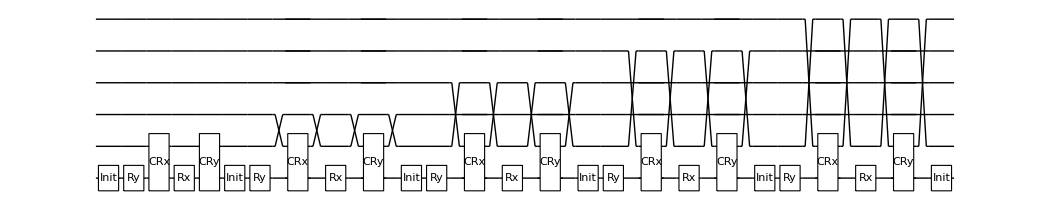

```mathematica
circInit={Subscript[initNcl, 1],Subscript[initNcl, 2],Subscript[initNcl, 3],Subscript[initNcl, 4],Subscript[initNcl, 5],Subscript[Init, 0]};
DrawCircuit[circInit]
```

```mathematica
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

```mathematica
SetQuregMatrix[ρ,RandomMixState[6]];
CalcFidelity[ρ,InitZeroState@ψ]
```

0.0168014

Initialization on the noisy circuit. Serialize[circ] removes parallelism in the circuit.

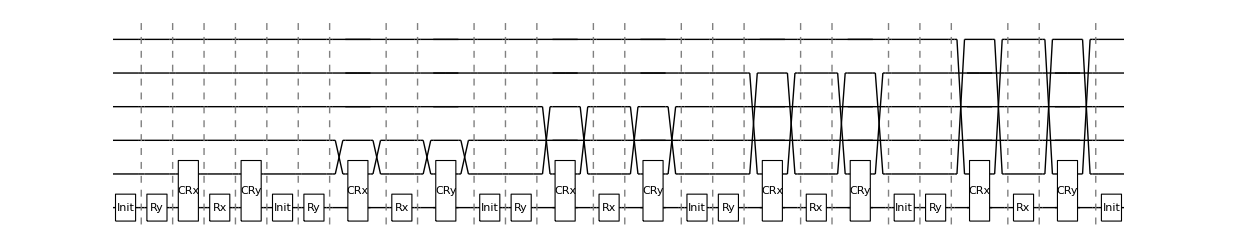

```mathematica
DrawCircuit@Serialize@circInit
```

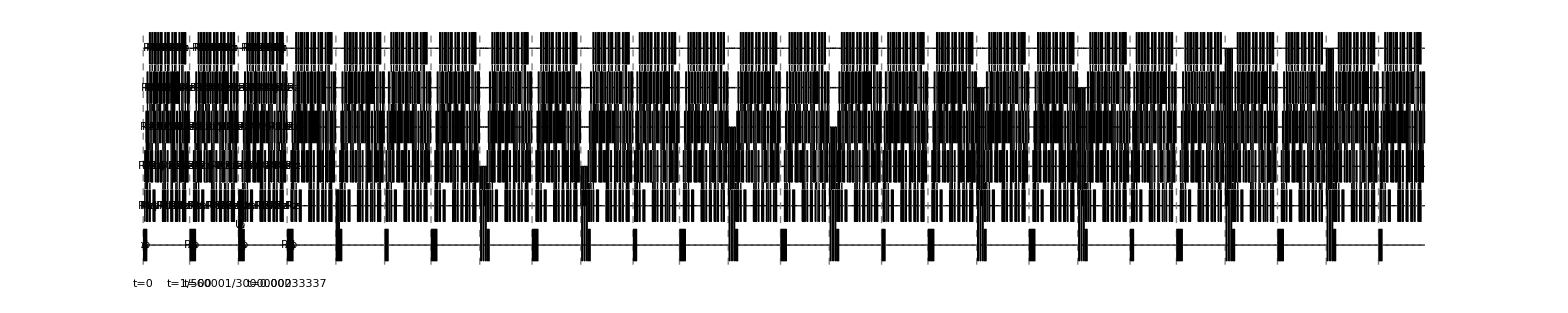

```mathematica
circInitOnDev=InsertCircuitNoise[Serialize@circInit,NVCenterDelft[],ReplaceAliases->True];
DrawCircuit[%,6]
```

```mathematica
ApplyCircuit[CloneQureg[ρ2,ρ],ExtractCircuit[circInitOnDev]];
CalcFidelity[ρ2,InitZeroState@ψ]
```

0.93252

```mathematica
DestroyAllQuregs[]
```

## Measurements

Measurements in the computational basis. Compare 4k shots of measurement to the fidelity set in the device

```mathematica
nshots=1000;
{ρ,ρinit}=CreateDensityQuregs[6,2];
```

#### On the electron spin

```mathematica
outputs=Flatten@Table[ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[M, 0]},NVCenterDelft[],ReplaceAliases->True]]
,{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total@outputs/nshots]*100]]
```

correct outputs(0):956
flipped outputs(1):44
fidelity:95.6

```mathematica
OptionValue[NVCenterDelft,FidMeas]
```

0.946

#### Measurement on the nuclear spins

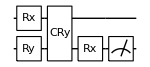

```mathematica
DrawCircuit[{Subscript[measZ, 1]}]
```

```mathematica
dev=NVCenterDelft[];
```

```mathematica
nshots=1000;
outputs=Flatten@Table[
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[measZ, 1]},NVCenterDelft[],ReplaceAliases->True]],{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total[outputs]/nshots]]]
```

correct outputs(0):930
flipped outputs(1):70
fidelity:0.93

### Trotterization-related modules

Reference:
https://aip.scitation.org/doi/10.1063/1.4768229

```mathematica
PauliCirc::usage="PauliCirc[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a term.";
PauliCirc[coef_,paulis_,nqubits_,factor_:1]:=Module[{circ,p,q,ngates},
If[Length@paulis>0,
circ=Table[
{p,q}=Level[c,-1];
Which[p===Z,{Subscript[C, q][Subscript[X, nqubits]]},p===X,{Subscript[Ry, q][π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Ry, q][-π/2]},p===Y,{Subscript[Rx, q][-π/2],Subscript[C, q][Subscript[X, nqubits]],Subscript[Rx, q][π/2]}]
,{c,paulis}];
Join[circ,{{Subscript[Rz, nqubits][coef*factor]}},Reverse@circ]
,
circ={}
]
]


Propagator::usage="Propagator[coefficient, pauli_list, nqubits, prefactor]. Return the circuit of a propagator.";
Propagator[coef_,paulis_,factor_]:=Module[{lpaulis,p,q,ngates,ops,ids,rops,ropsd,rcnot,j,i,pauliops},
rops={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][-π/2], Subscript[Z, _]:>{}};
ropsd={Subscript[X, j_]:>Subscript[H, j], Subscript[Y, j_]:>Subscript[Rx, j][π/2], Subscript[Z, _]:>{}};
rcnot={{i_Integer,j_Integer}:>Subscript[C, i][Subscript[X, j]] ,{{_Integer}}:>{} };
lpaulis=Table[{p,q}=Level[c,-1],{c,paulis}];
lpaulis=SortBy[lpaulis,#⟦2⟧&];
{ops,ids}={lpaulis⟦All,1⟧,Partition[lpaulis⟦All,2⟧,2,1]};
If[Length@ids<1, ids={lpaulis⟦All,2⟧}];
pauliops=Subscript[#⟦1⟧, #⟦2⟧]&/@lpaulis;
Flatten@{pauliops/.rops,ids/.rcnot,Subscript[Rz, Last@Last@ids][2*coef*factor],Reverse[ids/.rcnot],pauliops/.ropsd}
]


IsCommute::usage="IsCommute[List_paulis1, List_paulis2]. Return boolean indicates commutativity.";
IsCommute[P1_List,P2_List]:=Module[{m1,m2,nq,i},
nq=1+Max[Flatten@{P1,P2}/.Subscript[_, i_]->i];
m1=CalcCircuitMatrix[P1,nq];
m2=CalcCircuitMatrix[P2,nq];
If[Norm[m1.m2-m2.m1]≤10^-13,
True,
False]
]

PartitionPaulis::usage="ParititionPaulis[paulis], partition a list of pauli operators by commutation.";
PartitionPaulis[paulis_List]:=Module[{list1, list2},
list1={paulis⟦1⟧};list2={};
Table[
If[(AllTrue@@IsCommute[p⟦2;;⟧,#⟦2;;⟧]&/@list1)⟦1⟧,
AppendTo[list1,p],AppendTo[list2,p]]
,{p,paulis⟦2;;⟧}];
(*sanity checck*)
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list1,{2}]],
Print["ERR: there is a non-commuting operation in set A"]];
If[¬AllTrue[IsCommute[#⟦1⟧⟦2;;⟧,#⟦2⟧⟦2;;⟧]&/@Subsets[list2,{2}]],
Print["ERR: there is a non-commuting operation in set B"]];
{list1,list2}
]

Trotterize::usage="Trotterize[hamiltonian, t, n, order:1]. Return the trotterization circuit. Available up to the fourth order.
The paulis are partitioned into two sets A and B in which each element is commuting each other. 
Trotterization is available up to the 4th order
order 1: e^((A + B) t)=(e^(At/n)e^(Bt/n))^n+O(t Δt)
order 2: e^((A + B) t)=(e^(At/2  n)e^(Bt/n)e^(At/2  n))^n+O(t Δt^2)
order 2comp: is order 2 but compressed
order 2scb :(e^(At/2  n)e^(Bt/n)e^(At/2  n))(e^(Bt/2  n)e^(At/n)e^(Bt/2  n))(e^(At/2  n)e^(Bt/n)e^(At/2  n))
order 3: e^((A + B) t)=(e^(7/24)e^(2/3)e^(3/4)e^(-2/3)e^(-1/24)e^(Bt/n))^n+O(t Δt^3)
order 4: e^((A + B) t)=Π_(i = 1,  ... , 5)(e^p_ie^p_ie^p_i)^n+O(t Δt^4),where p1=p2=p4=p5=1/(4-4^(1/3)),p3=1-4p1
";
Trotterize[hamiltonian_,t_,n_,order_:1]:=Module[{list1,list2,Δt,f},
{list1,list2}=PartitionPaulis[List@@@List@@hamiltonian];
Which[
order===1,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===2,
f=N[0.5*t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
},{n}]
,
(*compressed2 -- check if it results in the circuit order 2
template: Flatten@{e^(A/2),e^B,Table[{e^A,e^B},{n-1}],e^(A/2)}
*)
order ==="2comp",
f=N[0.5*t/n];
Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[{Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}]},{n-1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]
}
,
(*simon's version of order 2*)
order==="2scb",
f=N[0.5*t/n];
Flatten@Table[
If[OddQ@iter,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list1}]}
,
{Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]}]
,{iter,n}] 
,
order===3,
f=N[t/n];
Flatten@Table[{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(7/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(2/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,(3/4)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-2)/3)f],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,((-1)/24)f],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,f],{p,list2}]
},{n}]
,
order===4,
f=ConstantArray[N[1/(4-4^(1/3))],5];
f⟦3⟧=N[1-4f⟦1⟧];
f=(0.5*t/n)*f;
Flatten@Table[
Flatten[Flatten@{
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,2#],{p,list2}],
Table[Propagator[p⟦1⟧,p⟦2;;⟧,#],{p,list1}]
}&/@f]
,{n}]
]
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
}
```

{t1→(9 ℏ)/J,t2→(18 ℏ)/J,Γ→0.1,ω→(5 J)/3}

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*{{0,8.9},{8.9,18.9,"spacing 0.1"},{18.9,27}}*)
```

```mathematica
(*ideal g*)
gdense={#,Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0)//.constants,J>0]}&/@Range[0,27,0.05];
```

```mathematica
(* Medium resolution: used in recompilation *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20,0.2],{20.,23.5,27}]
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

```mathematica
(* bit higher resulution for test the trotterisation methode used in the paper *)
τs=Sort@DeleteDuplicates@Chop@Join[Range[0.,8.,0.2],Range[8.,20.,0.1],{20.,27.,0.2}];
```

```mathematica
Length@%
```

162

```mathematica
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
```

True

```mathematica
(*τ=t J/ℏ*)
```

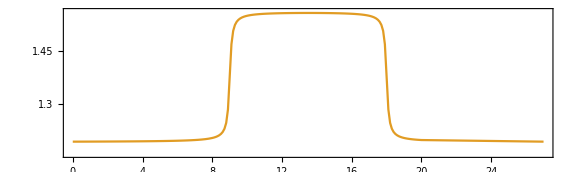

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[{gdense,Transpose@{τs,gvals}},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}},ImageSize->Large]
```

First part: Gaudin Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
(* Return the unitary of gaudin hamiltonian using MatrixExp *)
Ugaudin[n_,ϵ_,δt_,τ_]:=Module[{exp,g},
g=coupling[τ*ℏ/Δ0,g0,gc];
Table[
exp=ExpandAll@Simplify[(g*ϵ[[q+1]]*Hgaudin[q,n,ϵ,g]/ℏ)/.constants,J>0];
Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[I*δt*CalcPauliStringMatrix[ExpandAll[(exp*ℏ/Δ0) /. constants]]]]
,{q,0,n-1}]
]
(* Return the trotterized gaudin hamiltonian *)
Tgaudin[n_,ϵ_,δt_,τ_]:=Module[{exp,g,c},
g=coupling[τ*ℏ/Δ0,g0,gc];
SimplifyCircuit@Flatten@Table[
exp=SimplifyPaulis@ExpandAll@Simplify[((-g ϵ[[q+1]])/Δ0 Hgaudin[q,n,ϵ,g])/.constants,J>0];
Trotterize[exp,δt,TROTN,TROTO]
,{q,0,n-1}]
]
Tgaudin2[n_,ϵ_,δt_,τ_]:=Module[{exp,g,c},
g=coupling[τ*ℏ/Δ0,g0,gc];
exp=SimplifyPaulis@Total@Table[SimplifyPaulis@ExpandAll@Simplify[((-g ϵ[[q+1]])/Δ0 Hgaudin[q,n,ϵ,g])/.constants,J>0],{q,0,n-1}];
Trotterize[exp,δt,TROTN,TROTO]
]
```

Second part: Ising Hamiltonian

```mathematica
(* Return the unitary of ising hamiltonian using MatrixExp *)
Uising[δt_,τ_,n_]:=Module[{g=coupling[τ*ℏ/Δ0,g0,gc],exp},
exp=Flatten@Table[If[j!=k,Simplify[( g/(Δ0*4) If[And[j<n-1,k<n-1],Subscript[Z, j] Subscript[Z, k] Subscript[Id, n-1],Subscript[Z, j] Subscript[Z, k]])/.constants,J>0],{}],
{j,0,n-1},{k,0,n-1}];
Subscript[U, Sequence@@Range[0,n-1]][MatrixExp[-ⅈ δt CalcPauliStringMatrix[#]]]&/@exp
]
(* trotterized version *)
Tising[δt_,τ_,n_]:=Module[{g=coupling[τ*ℏ/Δ0,g0,gc]/Δ0,exp,α2},
α2=Simplify[( (δt g)/2)/.constants,J>0];
Flatten@Table[
If[j!=k,
(*Subscript[cnot, j,k] Subscript[R, k][2α] Subscript[cnot, j,k]*)
{Subscript[C, j][Subscript[X, k]],Subscript[Rz, k][α2],Subscript[C, j][Subscript[X, k]]}
,
{}],
{j,0,n-1},{k,0,n-1}]
]
```

Gaudin and Ising term -- per paper methode

```mathematica
Ising[n_,q_,δt_,τ_]:=With[{α2=Simplify[( (δt coupling[τ*ℏ/Δ0,g0,gc])/(2 Δ0))/.constants,J>0]},Table[{Subscript[C, q][Subscript[X, j]],Subscript[Rz, q][α2],Subscript[C, q][Subscript[X, j]]},{j,Complement[Range[0,n-1],{q}]}]]
```

```mathematica
TrotGaudinIsing[n_,ϵ_,δt_,τ_]:=Module[{exp,g,c,hgaudin,gcirc,icirc,totalcirc,α2},
g=coupling[τ*ℏ/Δ0,g0,gc];
(*Trotterize Gaudin term. The qubits are swapped by the end *)
totalcirc=Flatten@Table[
hgaudin=Total@Table[({Subscript[X, 0],Subscript[Y, 0],Subscript[Z, 0]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, 0]/g;
hgaudin=SimplifyPaulis@ExpandAll@Simplify[(-g*ϵ[[q+1]]*hgaudin/Δ0)/.constants,J>0];
gcirc=SimplifyCircuit@Trotterize[hgaudin,δt,TROTN,TROTO];
If[q<n-1,
AppendTo[gcirc,Subscript[SWAP, 0,q+1]]
];
gcirc
,{q,0,n-1}];

totalcirc=Join[totalcirc,
(* The Ising terms *)
Flatten@Table[
icirc=Ising[n,0,δt,τ];
If[q>0,
AppendTo[icirc,Subscript[SWAP, 0,q]]
];
icirc
,{q,n-1,0,-1}]
];
(*The last term *)
totalcirc=Join[totalcirc,Usingle[δt,τ,n]];

totalcirc
]
```

Third part: single qubits Hamiltonian

```mathematica
(* Return the unitary of single spin hamiltonian. The same with circuit. *)
Usingle[δt_,τ_,n_]:=Table[Subscript[Rz, j][Simplify[(δt/Δ0 coupling[τ*ℏ/Δ0,g0,gc])/.constants,J>0] ],{j,0,n-1}]
```

The entire BCS Hamiltonian

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0]
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0]
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0]
```

{1.30171 J,2.69258 J,4.28499 J,5.91843 J,7.56637 J}

{0.820092,0.964238,0.986194,0.992811,0.995614}

{0.179908,0.0357617,0.0138063,0.00718887,0.00438605}

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs
(* double check *)
2*ArcSin@Sqrt@vjs
```

{0.876058,0.380506,0.235545,0.169778,0.132552}

{0.876058,0.380506,0.235545,0.169778,0.132552}

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψmf,ψexact,ψinitmf,ψinitexact}=CreateQuregs[5,4];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];

(* mean field grounstate (product state) *)
ApplyCircuit[InitZeroState@ψinitmf,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
```

```mathematica
initv.initv//Chop
```

1.

Analytic solution: using MatrixExp[-ⅈ δtH_BCS]  vs trotter

```mathematica
δτ
```

{0,4.,4.,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,3.5,3.5}

```mathematica
(* Low resolution: 50 points *)
rexactot2<<rexactot2.mx;
(* high resolution 541 points *)
rexactot<<rexactot.mx;
```

```mathematica
Monitor[
τ=0;
CloneQureg[ψexact,ψinitexact];
rexactot2={{0,1}};
Table[
hbcs=CalcPauliStringMatrix@HBCS[5,ϵ,τ];
(*circ=Subscript[U, Sequence@@Range[0,4]][MatrixExp[-ⅈ δ hbcs ]];
*)
(*circ=Flatten@{TrotGaudinIsing[5,ϵ,δ,τ]};*)
ApplyCircuit[ψexact,circ];
τ+=δ;
AppendTo[rexactot2,{τ,CalcFidelity[ψinitexact,ψexact]}];
,{δ,δτ}];
,
ListPlot[{rexactot,rexactot2},Joined->{True,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ) up to τ="<>ToString[τ],ImageSize->Large,PlotRange->All]
]
```

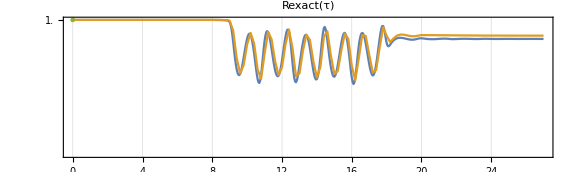

```mathematica
(*ListPlot[{gdense,Transpose@{τs,gvals}},Joined->{True,True},AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,3],None}},PlotLabel->"g(τ)",ImageSize->Large]*)
ListPlot[{rexactot,rexactot2,rexacttrot2},Joined->{True,True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```

```mathematica
DumpSave["rexactot.mx",rexactot];
```

Calculate Rmf using MatrixExp function and noiseless trotter

```mathematica
(* initialise *)
CloneQureg[ψmf,ψinitmf];
CloneQureg[ψexact,ψinitexact];

(* Rmf(τ)*)
(*τ=0;
rmf={{0,1}};
rexact={{0,1}};
Table[
τ+=δ;
bcscirc=Flatten@{Ugaudin[5,ϵ,δ,τ],Uising[δ,τ,5],Usingle[δ,τ,5]};
ApplyCircuit[ψmf,bcscirc];
ApplyCircuit[ψexact,bcscirc];
AppendTo[rmf,{τ,CalcFidelity[ψinitmf,ψmf]}];
AppendTo[rexact,{τ,CalcFidelity[ψinitexact,ψexact]}];
,{δ,δτ}];*)
```

```mathematica
nvcresults<<nvcresults.mx;
{rmf,rmftrot,rexact,rexacttrot}=Values@nvcresults;
τs=rmf[[All,1]];
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
```

```mathematica
gvals//Length
```

192

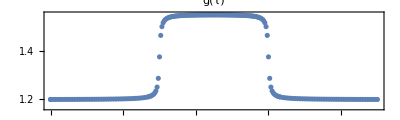

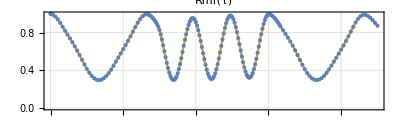

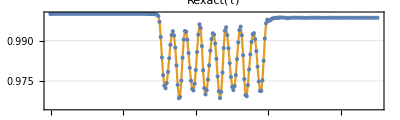

```mathematica
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->False,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,3],None}},PlotLabel->"g(τ)"]
ListPlot[{rmf,rmf},PlotRange->All,Joined->{False,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rmf(τ)"]
ListPlot[{rexact,rexact},PlotRange->{0.965,1},Joined->{False,True,False,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",FrameTicks->{{Automatic,None},{Range[0,27,3],None}}]
```

Using Trotterisation

```mathematica
(* initialise *)
CloneQureg[ψmf,ψinitmf];
CloneQureg[ψexact,ψinitexact];
TROTN=2;
TROTO=4;

(* Rmf(τ)*)
τ=0;
rmftrot={{0,1}};
rexacttrot={{0,1}};
bcstrotcircs={};
Table[
τ+=δ;
bcscirc=SimplifyCircuit@DeleteElements[Flatten@{Tgaudin2[5,ϵ,δ,τ],Tising[δ,τ,5],Usingle[δ,τ,5]},{Subscript[Rz, _][0.],Subscript[Rz, _][0],Subscript[Id, _][_]}];
AppendTo[bcstrotcircs,{τ,bcscirc}];
ApplyCircuit[ψmf,bcscirc];
ApplyCircuit[ψexact,bcscirc];
AppendTo[rmftrot,{τ,CalcFidelity[ψinitmf,ψmf]}];
AppendTo[rexacttrot,{τ,CalcFidelity[ψinitexact,ψexact]}];
,{δ,δτ}];
```

```mathematica
{rmf,rmftrot,rexact,rexacttrot}=Values@nvcresults;
```

```mathematica
(*nvcresults=<|"rmf"->rmf,"rmftrot"->rmftrot,"rexact"->rexact,"rexacttrot"->rexacttrot|>;
DumpSave["nvcresults.mx",nvcresults];*)
```

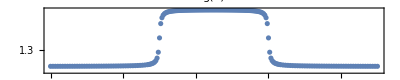

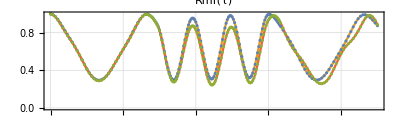

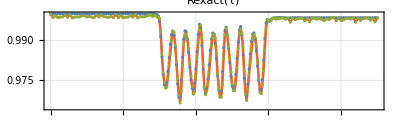

```mathematica
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->False,AspectRatio->0.2,Frame->True,FrameTicks->{{Range[1,1.55,0.1],None},{Range[0,27,3],None}},PlotLabel->"g(τ)",ImageSize->400]
ListPlot[{rmf,rmf,rmftrot,rmftrot},PlotRange->All,Joined->{False,True,False,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rmf(τ)",ImageSize->400]
ListPlot[{rexact,rexact,rexacttrot,rexacttrot},PlotRange->All,Joined->{False,True,False,True},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->400]
```

```mathematica
bcstrotcircs<<bcstrotcircs.mx;
```

```mathematica
hbcsmat0=CalcPauliStringMatrix@hbcs0;
hbcsmat1=CalcPauliStringMatrix[HBCS[5,ϵ,2.0]];
```

```mathematica
ψ=CreateQureg[5];
```

```mathematica
ApplyCircuit[InitZeroState@ψ,Subscript[X, #]&/@{0,3,4}]
```

{}

```mathematica
ApplyCircuit[ψ,Subscript[U, Sequence@@Range[0,4]][MatrixExp[-ⅈ hbcsmat1 0.1]]]
```

{}

Convert  Trotterised circuits to the native NV-center gates

```mathematica
(* minimize the rotation angle *)
round2pi[θ_]/;θ>=0:=With[{ϕ=Mod[θ,2π]},If[Abs[2π-ϕ]<ϕ,-(2π-ϕ),ϕ]]
replaceθ={
Subscript[Rz, q_][θ_]/;θ>=0:>Subscript[Rz, q][Chop@round2pi[θ]],
Subscript[Rx, q_][θ_]/;θ>=0:>Subscript[Rx, q][Chop@round2pi[θ]],
Subscript[Ry, q_][θ_]/;θ>=0:>Subscript[Ry, q][Chop@round2pi[θ]]
};
```

```mathematica
swapCRx[g_]:=Module[{i,j,θ,circ},
{i,j,θ}=g/.Subscript[CRx, p_,q_][t_]:>{p,q,t};
circ=Which[
(i==0)&&(j>0),
{Subscript[CRx, 0,j][θ]}
,
(i>0)&&(j>0)
,
{Subscript[SWAP, 0,i],Subscript[CRx, 0,j][θ],Subscript[SWAP, 0,i]}/.swaprep
,
(*i>0, j=0*)
True,
{Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π],Subscript[CRx, 0,i][θ],Subscript[Ry, i][π/2],Subscript[Rx, i][π],Subscript[Ry, j][π/2],Subscript[Rx, j][π]}
];
Sequence@@circ
]
```

```mathematica
swaprep={Subscript[SWAP, c_,t_]:>Sequence@@{Subscript[CRx, c,t][π/2],Subscript[Rx, t][π/2],Subscript[Rz, c][π/2],Subscript[CRx, c,t][π/2],Subscript[Rx, t][-π/2],Subscript[Rz, c][π/2],Subscript[CRx, c,t][π/2],Subscript[Rz, c][π/2],Subscript[Rx, t][π/2]}};
nvcnative={
Subscript[C, c_][Subscript[X, t_]]:>Sequence@@{swapCRx[Subscript[CRx, c,t][π/2]],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]},
Subscript[H, q_]:>Sequence@@{Subscript[Ry, q][π/2],Subscript[Rx, q][π]},
Subscript[CRx, c_,t_][θ_]:>swapCRx[Subscript[CRx, c,t][θ]]
};
```

```mathematica
(* simple gate merges *)
mergeNVCGates[longcirc_]:=Module[{circ,circcol,a,b,c,d,e,f,i,j,slen,k,l,θmerge={},deleted=0},
circ=longcirc;
While[True,
slen=Length@circ;
circcol=GetCircuitColumns[circ];
(* simplify parametric gates *)
circcol=circcol//.{
{a___,{b___,Subscript[Rx, j_][θ1_],c___},{d___,Subscript[Rx, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rx, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Ry, j_][θ1_],c___},{d___,Subscript[Ry, j_][θ2_],e___},f___}:>{a,{b,Subscript[Ry, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[Rz, j_][θ1_],c___},{d___,Subscript[Rz, j_][θ2_],e___},f___}:>{a,{b,Subscript[Rz, j][θ1+θ2],c},{d,e},f},
{a___,{b___,Subscript[CRx, i_,j_][θ1_],c___},{d___,Subscript[CRx, i_,j_][θ2_],e___},f___}:>{a,{b,Subscript[CRx, i,j][θ1+θ2],c},{d,e},f}
};
circ=DeleteElements[Flatten[circcol]/.replaceθ,{Subscript[_, __][0],Subscript[_, __][0.]}];
If[Length@circ==slen,Break[]];
];
circ
]
```

Convert all gates into the NVC native gates

```mathematica
bcstrotcircs<<bcstrotcircs.mx;
```

```mathematica
bcstrotnvc={{0,{}}};
```

```mathematica
Table[
{τ,circ}=bcstrotcircs[[j]];
AppendTo[bcstrotnvc,
{τ,mergeNVCGates[circ/.replaceθ/.nvcnative]}
]
,{j,2,Length@bcstrotcircs}];
```

```mathematica
DumpSave["bcstrotnvc.mx",bcstrotnvc];
```

Emulation on a noisy NV-center device

```mathematica
Options[NVCenterDelft]={
qubitsNum->5,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60 |>,
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9|>,
GlobalField-><|#->RandomReal[{-0.01,0.01}]&/@Range[0,4]|>,
GlobalFieldDetuning->66000,
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500|>,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3|>,
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 |>,
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 |>,
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99 |>,
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.9999 |>,
EFSingleXY->{0.75,0.25},
EFCRot->{0.9,0.1},
FidInit-> 0.999,
DurInit->2*10^-3,
FidMeas->0.946,
DurMeas->2*10^-5
};
```

```mathematica
nvcresults<<nvcresults.mx;
```

```mathematica
circ=bcstrotcircs[[2,2]]/.nvcnative/.replaceθ
```

```mathematica
Length@circ
```

15574

```mathematica
DeleteElements[circ,{Subscript[H, _]}]//Length
```

15574

```mathematica
Length@circ
```

15574

```mathematica
mcirc=mergeNVCGates[circ]
```

```mathematica
mcirc=%;
```

```mathematica
mcirc2=DeleteElements[mcirc,{Subscript[_, __][0.],Subscript[_, __][0]}]
```

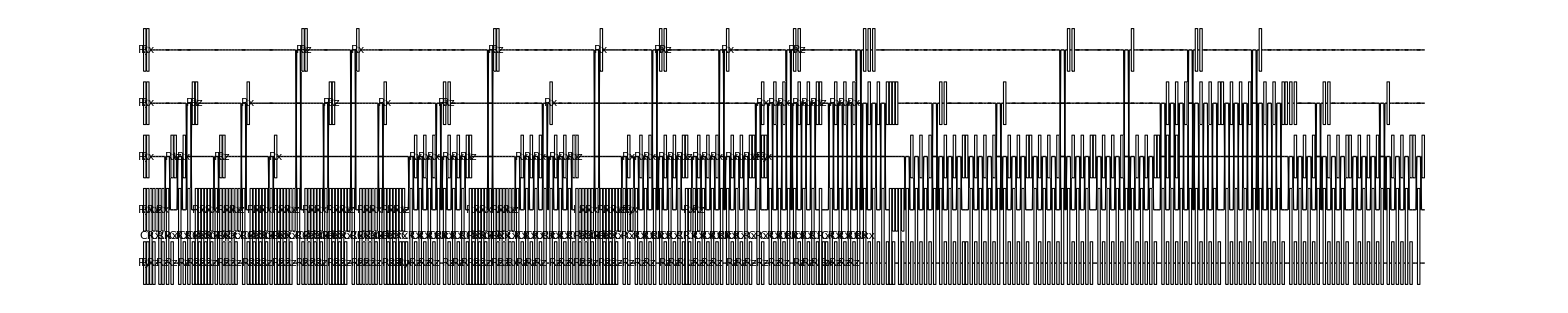

```mathematica
DrawCircuit@mcirc[[;;500]]
```

```mathematica
mcirc2//Length
```

15314

```mathematica
ncirc=InsertCircuitNoise[mcirc,NVCenterDelft[]];
```

```mathematica
ncirc2=DeleteElements[Chop@ExtractCircuit[ncirc],{Subscript[_, __][0.],Subscript[_, __][0]}];
```

$Aborted

```mathematica
Length@ncirc2
```

133168

```mathematica
DestroyAllQuregs[]
{ρmf,ρexact,ρinitmf,ρinitexact}=CreateDensityQuregs[5,4];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=List/@eigvec[[First@Ordering[eigval,1]]];
```

```mathematica
SetQuregMatrix[ρinitexact,initv.ConjugateTranspose[initv]]
```

3

```mathematica
(* mean field grounstate (product state) *)
ApplyCircuit[InitZeroState@ρinitmf,Table[Subscript[Ry, j-1][θinit[[j]]],{j,5}]];
```

```mathematica
ExtractCircuit@InsertCircuitNoise[bcstrotnvc[[2,2]],NVCenterDelft[]]
```

InsertCircuitNoise::error: Encountered gate H_1 which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

$Failed

```mathematica
(* initialise *)
CloneQureg[ρmf,ρinitmf];
CloneQureg[ρexact,ρinitexact];

(* Rmf(τ)*)
rmftrot={{0,1}};
rexacttrot={{0,1}};
bcstrotcircs={};
Table[
{τ,bcscirc}=circ;
If[τ>0,
noisycirc=InsertCircuitNoise[bcscirc];
ApplyCircuit[ψmf,bcscirc];
ApplyCircuit[ψexact,bcscirc];
AppendTo[rmftrot,{τ,CalcFidelity[ψinitmf,ψmf]}];
AppendTo[rexacttrot,{τ,CalcFidelity[ψinitexact,ψexact]}];
]
,{circ,bcscircs}];
```

```mathematica
{rmf,rmftrot,rexact,rexacttrot}=Values@nvcresults;
```